10 Límites
10.1 Noción intuitiva de límite

```mathematica
f[x_]:=Sin[x]/x
f[0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
N[f[1/10],20]
N[f[1/1000],20]
N[f[1/100000],20]
```

0.99833416646828152307

0.99999983333334166667

0.99999999998333333333

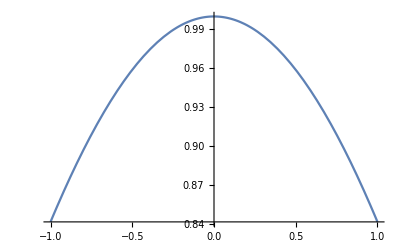

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
Limit[f[x],x->0]
```

1

```mathematica
Limit[Abs[x]/x,x->0] (* Se calcula el límite por la derecha, por defecto *)
```

Indeterminate

```mathematica
Limit[Abs[x]/x,x->0,Direction->-1] (* Límite por la derecha *)
```

1

```mathematica
Limit[Abs[x]/x,x->0,Direction->1] (* Límite por la izquierda *)
```

-1

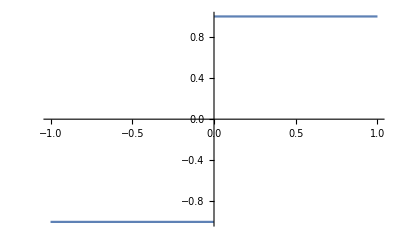

```mathematica
Plot[Abs[x]/x,{x,-1,1}] (* Se aprecia la discontinuidad *)
```

10.2 Indeterminaciones

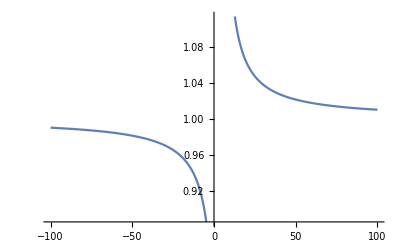

```mathematica
Plot[(x^2-5x+6)/(x^2-6x+8),{x,-100,100}] (* Asíntota horizontal *)
```

```mathematica
Limit[(x^2-5x+6)/(x^2-6x+8),x->Infinity] (* Asíntota horizontal igual a 1 *)
```

1

```mathematica
Limit[(1+x/n)^n,n->Infinity]
```

ⅇ^x

```mathematica
Limit[(x-16)/(Sqrt[x]-4),x->16] (* Ejes del mismo tamaño *)
```

8

10.3 Derivadas como límites

```mathematica
Limit[(Cos[x+h]-Cos[x])/h,h->0]
```

-Sin[x]

10.4 Continuidad

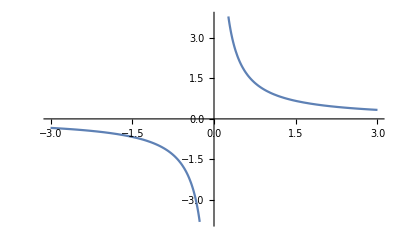

```mathematica
Plot[1/x,{x,-3,3}]
```

```mathematica
Limit[1/x,x->0,Direction->-1] 
Limit[1/x,x->0,Direction->1] (* No es continua por tener límites laterales distintos *)
```

∞

-∞

```mathematica
Limit[(2+x)^(1/x),x->0,Direction->-1] 
Limit[(2+x)^(1/x),x->0,Direction->1] (* No es continua por tener límites laterales distintos *)
```

∞

0

10.5 Asíntotas

```mathematica
f[x_]:=(2x^2-6x+3)/(x-4)
```

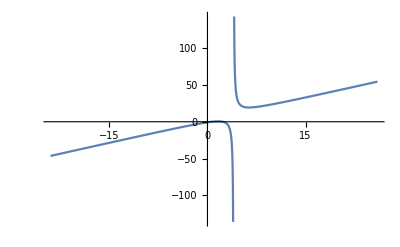

```mathematica
Plot[f[x],{x,-24,26}] (* Tiene asíntota vertical y oblicua, pero no horizontal *)
```

```mathematica
Limit[f[x],x->Infinity](* No tiene asíntota horizontal *)
```

∞

```mathematica
m=Limit[f[x]/x,x->Infinity](* Tiene asíntota oblicua con pendiente 2 *)
```

2

```mathematica
s=Limit[f[x]-m*x,x->Infinity](* Tiene asíntota oblicua con ordenada al origen en f(0)=2 *)
```

2

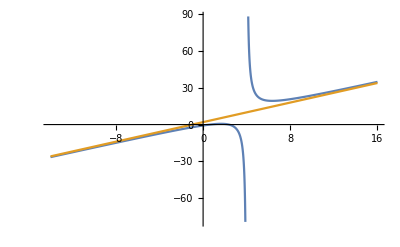

```mathematica
Plot[{f[x],2x+2},{x,-14,16}]
```

```mathematica
Limit[f[x],x->4, Direction->-1]
Limit[f[x],x->4, Direction->1](* Tiene asintota vertical *)
```

∞

-∞

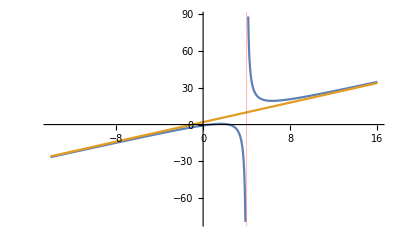

```mathematica
Plot[{f[x],2x+2},{x,-14,16},GridLines->{{{4,Red}},None}]
```